```mathematica
SGD[ng_]:=(θ-=αm*ng);                                                                       (* step of vanilla SGD *)
ADAM[ng_]:=(t++;m=β1*m+(1-β1)ng;vv=β2*vv+(1-β2)ng^2; (* ADAM *)
θ-=α*m/((ϵ+Sqrt[vv/(1-β2^t)])*(1-β1^t)));            (* arXiv:1412.6980 *)  
init[d_]:=(m=mg=mθ=vv=0.;V=RandomReal[0.001,{d,𝔇}];
dgg=dθθ=0.1;mgg=mθθ=0.1*IdentityMatrix[d];t=0;SeedRandom[seed]);
sm[M_]:=M+Transpose[M];noise:=RandomReal[NormalDistribution[0,σ],𝔇];    
cdOGR[ng_]:=(mθ+=β(θ-mθ);mg+=β(ng-mg);m+=γ(ng-m);(* diagonal Hessian *)
dθθ+=β((θ-mθ)^2-dθθ);dgg+=β((ng-mg)^2-dgg);                    (* update averages *)
θ-=η*Map[Min[#,maxα]&,Sqrt[dθθ/dgg]*m]);                                      (* Newton step *)
eh[lm_]:=1/Map[Max[#,cut]&,Abs[lm]]; (* eigenvalue inv, div&cut *)
ma[A_]:=({e,ev}=Eigensystem[A];Transpose[ev].DiagonalMatrix[eh[e]].ev);
cfOGR[ng_]:=(m+=γ(ng-m);mθ+=β(θ-mθ);mg+=β(ng-mg);         (* full Hessian *)
mθθ+=β(KroneckerProduct[θ-mθ,θ-mθ]-mθθ);{e,ev}=Eigensystem[mθθ]; 
mgg+=β(KroneckerProduct[ng-mg,ng-mg]-mgg);
σθ=MatrixFunction[Sqrt,mθθ];σg=MatrixFunction[Sqrt,mgg];
pH=Transpose[ev].((ev.sm[σθ.σg].Transpose[ev])/sm[Table[e,𝔇]]).ev;(*Hessian*) 
θ-=η*ma[pH].m);           
csOGR[ng_]:=(mθ+=β(θ-mθ);mg+=β(ng-mg);m+=γ(ng-m);     (* dim d subspace *)
V=Orthogonalize[Table[v+Γ*ng,{v,V}]];                       (* explore new directions *)
pθ=V.(θ-mθ);pg=V.(ng-mg);                            (* mean subtractions & projections *)                                                   
mθθ+=β(KroneckerProduct[pθ,pθ]-mθθ); {e,ev}=Eigensystem[mθθ];
mgg+=β(KroneckerProduct[pg,pg]-mgg); 
σθ=MatrixFunction[Sqrt,mθθ];σg=MatrixFunction[Sqrt,mgg];
pH=Transpose[ev].((ev.sm[σθ.σg].Transpose[ev])/sm[Table[e,d]]).ev;(*Hessian*) 
θ-=η*(ma[pH].(V.m)).V);  (* Newton in V subspace*)
cdsOGR[ng_]:=(mθ+=β(θ-mθ);mg+=β(ng-mg);m+=γ(ng-m);   (*diagonal+subspace*)
dθθ+=β((θ-mθ)^2-dθθ);dgg+=β((ng-mg)^2-dgg);                     (* diagonal updates *)
V=Orthogonalize[Table[v+Γ*ng,{v,V}]];                         (* explore new directions *)
pθ=V.(θ-mθ);pg=V.(ng-mg);                              (* mean subtractions & projections *)                                                 
mθθ+=β(KroneckerProduct[pθ,pθ]-mθθ); {e,ev}=Eigensystem[mθθ];
mgg+=β(KroneckerProduct[pg,pg]-mgg); 
σθ=MatrixFunction[Sqrt,mθθ];σg=MatrixFunction[Sqrt,mgg];
pH=Transpose[ev].((ev.sm[σθ.σg].Transpose[ev])/sm[Table[e,d]]).ev;(*Hessian*) 
Δθ=η*Map[Min[#,maxα]&,Sqrt[dθθ/dgg]*m];                  (* diagonal Hessian step*)
θ-=Δθ-w(Δθ.Transpose[V].V-η*(ma[pH].(V.m)).V));

(* function: 3D Beale, gradient simulation parameters *)
b=(1.5-x+x*y)^2+(2.25-x+x*y^2)^2+(2.625-x+x*y^3)^2;(* Beale function *)
f=Simplify[b+(b/.x->z)];v={x,y,z};𝔇=Length[v];(*3D:b(x,y)+b(z,y)*)
𝔇=3;sub[p_]:=Table[v[[i]]->p[[i]],{i,𝔇}];g=Grad[f,v];
ϵ=10^-6;σ=0.1; steps=50;r=3; seed=1; (* simulation parameters *)
```

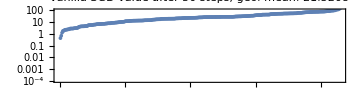

```mathematica
αm=0.0002; (* vanilla SGD *)
eval=Sort[Flatten[Table[init[𝔇];θ={sx,sy,sz};
Do[SGD[(g/.sub[θ])+noise],{i,steps}];f/.sub[θ],{sx,-r,r},{sy,-r,r},{sz,-r,r}]]];
ListLogPlot[eSGD=eval,PlotRange->{0.0001,100},PlotTheme->"Detailed",AspectRatio->1/4,ImageSize->Medium,PlotLabel->Row[{"vanilla SGD value after ",steps," steps, geo. mean: ",Exp[Mean[Log[eval]]]}]]
```

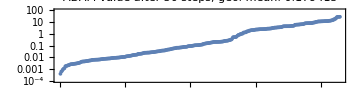

```mathematica
α=0.7;β1=0.8;β2=0.9; (* ADAM *)
eval=Sort[Flatten[Table[init[𝔇];θ={sx,sy,sz};
Do[ADAM[(g/.sub[θ])+noise],{i,steps}];f/.sub[θ],{sx,-r,r},{sy,-r,r},{sz,-r,r}]]];
ListLogPlot[eADAM=eval,PlotRange->{0.0001,100},PlotTheme->"Detailed",AspectRatio->1/4,ImageSize->Medium,PlotLabel->Row[{"ADAM value after ",steps," steps, geo. mean: ",Exp[Mean[Log[eval]]]}]]
```

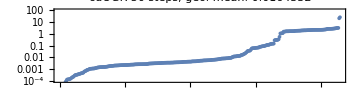

```mathematica
β=0.4;γ=0.5;η=0.6;maxα=Infinity; (* cdOGR *)
eval=Sort[Flatten[Table[init[𝔇];θ={sx,sy,sz};
Do[cdOGR[(g/.sub[θ])+noise],{i,steps}];f/.sub[θ],{sx,-r,r},{sy,-r,r},{sz,-r,r}]]];
ListLogPlot[ecdOGR=eval,PlotRange->{0.0001,100},PlotTheme->"Detailed",AspectRatio->1/4,ImageSize->Medium,PlotLabel->Row[{"cdOGR ",steps," steps, geo. mean: ",Exp[Mean[Log[eval]]]}]]
```

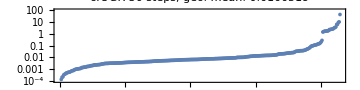

```mathematica
β=0.7;γ=0.7;η=1;cut=5; (* cfOGR *)
eval=Sort[Flatten[Table[init[𝔇];θ={sx,sy,sz};
Do[cfOGR[(g/.sub[θ])+noise],{i,steps}];f/.sub[θ],{sx,-r,r},{sy,-r,r},{sz,-r,r}]]];
ListLogPlot[ecfOGR=eval,PlotRange->{0.0001,100},PlotTheme->"Detailed",AspectRatio->1/4,ImageSize->Medium,PlotLabel->Row[{"cfOGR ",steps," steps, geo. mean: ",Exp[Mean[Log[eval]]]}]]
```

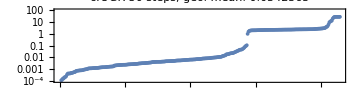

```mathematica
Γ=0.1;β=0.7;γ=0.7;η=0.9;cut=10; d=1;(* d=1 csOGR *)
eval=Sort[Flatten[Table[init[d];θ={sx,sy,sz};
Do[csOGR[(g/.sub[θ])+noise],{i,steps}];f/.sub[θ],{sx,-r,r},{sy,-r,r},{sz,-r,r}]]];
ListLogPlot[ecs1OGR=eval,PlotRange->{0.0001,100},PlotTheme->"Detailed",AspectRatio->1/4,ImageSize->Medium,PlotLabel->Row[{"cfOGR ",steps," steps, geo. mean: ",Exp[Mean[Log[eval]]]}]]
```

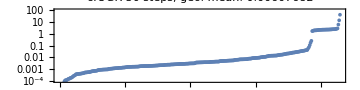

```mathematica
Γ=0.2;β=0.7;γ=0.7;η=1;cut=5; d=2;(* d=2 csOGR *)
eval=Sort[Flatten[Table[init[d];θ={sx,sy,sz};
Do[csOGR[(g/.sub[θ])+noise],{i,steps}];f/.sub[θ],{sx,-r,r},{sy,-r,r},{sz,-r,r}]]];
ListLogPlot[ecs2OGR=eval,PlotRange->{0.0001,100},PlotTheme->"Detailed",AspectRatio->1/4,ImageSize->Medium,PlotLabel->Row[{"cfOGR ",steps," steps, geo. mean: ",Exp[Mean[Log[eval]]]}]]
```

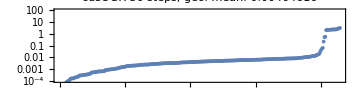

```mathematica
Γ=0.1;β=0.7;γ=0.7;η=1; w=0.5;d=1;maxα=Infinity;cut=0.0001;(* d=1 cdsOGR, maxα for 'd', cut for 's' *)
eval=Sort[Flatten[Table[init[d];θ={sx,sy,sz};
Do[cdsOGR[(g/.sub[θ])+noise],{i,steps}];f/.sub[θ],{sx,-r,r},{sy,-r,r},{sz,-r,r}]]];
ListLogPlot[ecds1OGR=eval,PlotRange->{0.0001,100},PlotTheme->"Detailed",AspectRatio->1/4,ImageSize->Medium,PlotLabel->Row[{"cdsOGR ",steps," steps, geo. mean: ",Exp[Mean[Log[eval]]]}]]
```

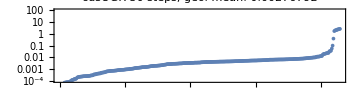

```mathematica
Γ=0.1;β=0.7;γ=0.7;η=1.; w=0.5;d=2;maxα=Infinity;cut=0.0001;(* d=2 cdsOGR, maxα for 'd', cut for 's' *)
eval=Sort[Flatten[Table[init[d];θ={sx,sy,sz};
Do[cdsOGR[(g/.sub[θ])+noise],{i,steps}];f/.sub[θ],{sx,-r,r},{sy,-r,r},{sz,-r,r}]]];
ListLogPlot[ecds2OGR=eval,PlotRange->{0.0001,100},PlotTheme->"Detailed",AspectRatio->1/4,ImageSize->Medium,PlotLabel->Row[{"cdsOGR ",steps," steps, geo. mean: ",Exp[Mean[Log[eval]]]}]]
```

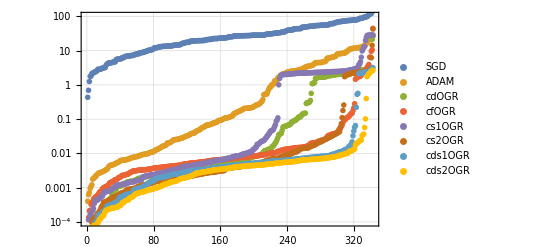

```mathematica
ListLogPlot[{eSGD,eADAM,ecdOGR,ecfOGR,ecs1OGR,ecs2OGR,ecds1OGR,ecds2OGR},PlotRange->{0.0001,100},PlotStyle->PointSize[0.01],PlotLegends->{"SGD","ADAM","cdOGR","cfOGR","cs1OGR","cs2OGR","cds1OGR","cds2OGR"},PlotTheme->"Detailed"]
```